```mathematica
ClearAll[c,G,MSun,rhoRadBBN];

c=29979245800;                   (*velocidad de la luz:cm/s*)
G=66743/10^12;                   (*constante gravitacional:cm^3/(g s^2)*)
MSun=198847*10^28;               (*masa solar:g*)

rhoRadBBN=7331305019814086*10^11;
(*densidad de energía de radiación en BBN:erg/cm^3*)
```

```mathematica
ti=37/50;                       (*coordenada temporal de BBN:0.74 s*)
ai=83/500000000000;             (*factor de escala en BBN:1.66*10^-10*)
Hti=67/100;                     (*parámetro de Hubble en BBN:0.67 s^-1*)
```

```mathematica
ρ0[ξ_]:= ξ*rhoRadBBN
```

```mathematica
Cxi[ξ_]:= (4π G)/(3c^2)*ρ0[ξ]
```

```mathematica
ClearAll[sol];
```

```mathematica
tMin=-5;
(* n = -1 luego 
(Y[t])^((n-1)/2) ----> Y^-1
*)
```

```mathematica
ClearAll[sol,tBounce]
```

```mathematica
sol[ξ_]:=sol[ξ]=NDSolve[{Y'[t]==v[t],v'[t]==2*Cxi[ξ]*(Y[t])^(-1),Y[ti]==1,v[ti]==2*Hti},{Y,v},{t,tMin,ti},WorkingPrecision->40,AccuracyGoal->25,PrecisionGoal->25,
Method->"StiffnessSwitching",MaxSteps->Infinity ];
```

```mathematica
Yfunc[ξ_,t_]:=Y[t]/. sol[ξ][[1]];
vFunc[ξ_,t_]:=v[t]/. sol[ξ][[1]];
```

```mathematica
apos1[ξ_, t_] := ai*√Yfunc[ξ, t]
```

```mathematica
sol[1/10];
```

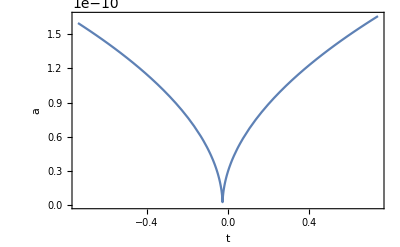

```mathematica
Plot[apos1[1/10, t], {t, -ti, ti}, AxesLabel->{t,a},Frame->True, PlotRangePadding->0 ]
```

```mathematica
ClearAll[tBounce]
```

```mathematica
tBounce[ξ_]:=tBounce[ξ]=t/. FindRoot[vFunc[ξ,t]==0,{t,0,-0.1},WorkingPrecision->40];
```

```mathematica
tB= tBounce[1/10]
```

-0.02689614804677555169789972464962459537388

```mathematica
apos[ξ_, t_]:=ai*Sqrt[Y[t+tBounce[ξ]]/. sol[ξ][[1]]];
```

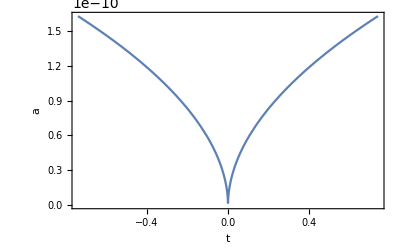

```mathematica
Plot[apos[1/10, t], {t, -ti, ti}, AxesLabel->{t,a},Frame->True, PlotRangePadding->0 ]
```

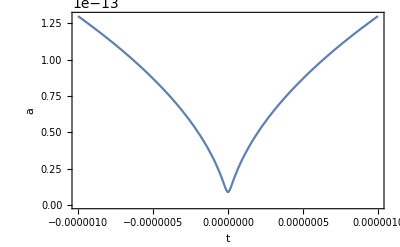

```mathematica
Plot[apos[1/10, t], {t, -1/1000000, 1/1000000}, AxesLabel->{t,a},Frame->True, PlotRangePadding->0 ]
```

```mathematica
ar := ai/ti^(1/2)
aRad[t_]:= ar*t^(1/2)
```

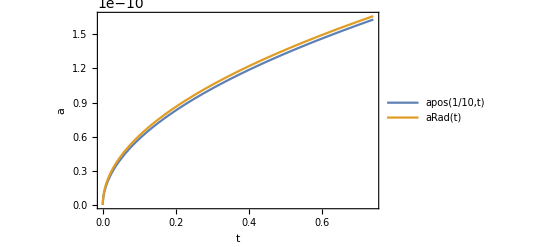

```mathematica
Plot[{apos[1/10, t],aRad[t]},{t,0,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0, PlotLegends->"Expressions"]
```

```mathematica
ρbh[ξ_,t_]:= ρ0[ξ]*(ai/apos[ξ, t])^4
```

```mathematica
Plot[ρbh[1/10, t],{t,-ti,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
ρbh[1/10,0]
```

9.17161253809042778849880825973955×10^42

```mathematica
ρbh[1/10, 10^(-4)]
```

8.65610097086653897201364228691905459×10^33

```mathematica
DotA[ξ_, t_] := (ai^2*vFunc[ξ, t+tBounce[ξ]])/(2*apos[ξ, t])
```

```mathematica
DotA[1/10, 0]
```

0.

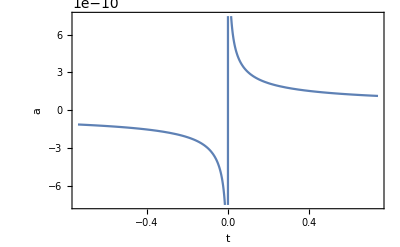

```mathematica
Plot[DotA[1/10, t],{t,-ti,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

```mathematica
ρrad[ξ_, t_]:= (3c^2)/(8π G)(DotA[ξ, t]/apos[ξ, t])^2 -ρbh[ξ, t]
```

```mathematica
Plot[ρrad[1/10, t],{t,-ti, ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
ρrad[1/10, 10^(-4)]
```

3.63164438535626669409879208478859094×10^34

```mathematica
ρrad[1/10, 0]
```

-9.17161253809042778849880825973955×10^42

```mathematica
Plot[ρrad[1/10, t],{t,-10^(-6),10^(-6)},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
HubbleParameter[ξ_, t_]:= √((8π G)/(3c^2)(ρrad[ξ, t]+ρbh[ξ, t]))
```

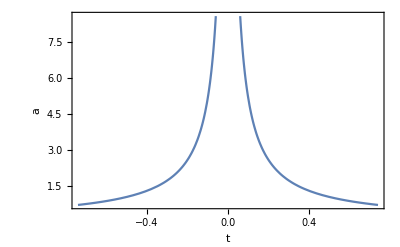

```mathematica
Plot[HubbleParameter[1/10, t],{t,-ti,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

```mathematica
Plot[HubbleParameter[1/10, t],{t,-10^(-7),10^(-7)},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

```mathematica
HubbleParameter[1/10, 0]
```

0.

```mathematica
Plot[ρrad[1/10, t]+ρbh[1/10, t],{t,-10^(-7),10^(-7)},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
HubbleParameter[1/10, 10^(-4)]
```

5289.50696158741427419083224305513042

```mathematica
5289.5069615874142741908322430551304151016512783262747604315714`36.94221133658748/5000
```

1.05790139231748285483816644861102608

```mathematica
MHubble[ξ_, t_]:= (4π c)/3*(ρrad[ξ, t]+ρbh[ξ, t])/(HubbleParameter[ξ, t])^3
```

```mathematica
Plot[MHubble[1/10, t],{t,-10^(-7),10^(-7)},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
γ := 0.2
Minic[ξ_, t_] := γ*MHubble[ξ, t]
```

```mathematica
Minic[1/10, 10^(-4)]
```

7.63205×10^33

```mathematica
Minic[1/10,10^(-4)]/MSun
```

3.83815

```mathematica
β = ρbh[1/10, 10^(-4)]/(ρrad[1/10, 10^(-4)]+ρbh[1/10, 10^(-4)])
```

0.192475231380825083117352215009114906

```mathematica
xiCompareValues=10^-Range[10];
```

```mathematica
tForm=10^(-4);
```

```mathematica
tablaDatos=N[Table[{xi,HubbleParameter[xi,tForm],MHubble[xi,tForm],Minic[xi,tForm],ρbh[xi,tForm]/(ρrad[xi,tForm]+ρbh[xi,tForm])},{xi,xiCompareValues}],18];
```

InterpolatingFunction::dmval: Input value {-0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-0.1} and/or the interpolation grid is insufficient to compute the value.

FindRoot::nlnum: The function value {«1»} is not a list of numbers with dimensions {1} at {t} = {-0.1}.

InterpolatingFunction::dmval: Input value {-0.0999} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-0.0999} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-0.0999} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-0.0999} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

FindRoot::nlnum: The function value {«1»} is not a list of numbers with dimensions {1} at {t} = {-0.1}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.